```mathematica
mecca = {"Mecca",  "SaudiArabia"};
petra = {"Wadi Musa", "Jordan"};
jerusalem = {"Jerusalem", "Israel"};
```

```mathematica
direction=GeoDirection@@Map[#~CityData~"Coordinates"&,{##}]&;
```

```mathematica
compareQibla[city_, orientation_ : 0] := Module[
{a, o=Point@{0,0}, g={Red,Green,Blue,Gray}, q},
a=Arrow@AnglePath[{π/2-#}]&;
q=Riffle[g,{"Mecca","Petra","Jerusalem"}];
g=Riffle[g, a@direction[city,#]&/@{mecca,petra,jerusalem}];
If[orientation!=0,o=a[orientation];q~AppendTo~"Mosque Orientation"];
g=Graphics[Flatten@Insert[{Thick,o,Dashed,Thin,Circle[]},g,2],
ImageSize->Medium,PlotLabel->city~StringRiffle~", "];
Row@{g, LineLegend@@Transpose@Partition[q,2]}]
```

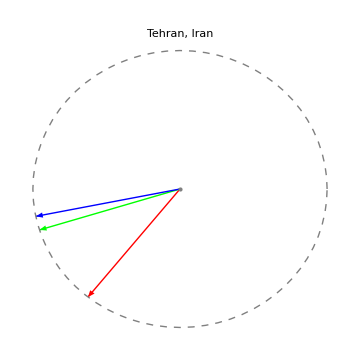

```mathematica
compareQibla[{"Tehran","Iran"}]
```

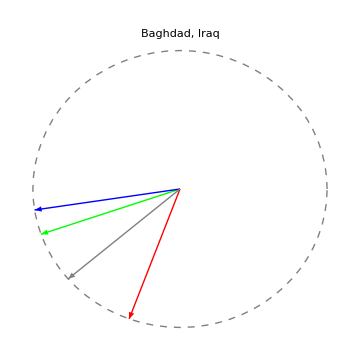

```mathematica
compareQibla[{"Baghdad","Iraq"},229.5°]
```